Mecánica Vectorial - Tarea 1 (Ejercicio 7) - Briones Andrade Joshua

1) Movimiento Oscilatorio a lo largo de X (ω = 1)

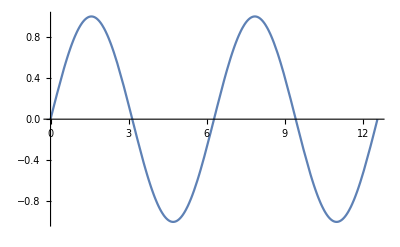

```mathematica
posic1=Plot[Sin[ ω x]/. ω-> 1,{x,0, 4 Pi}]
```

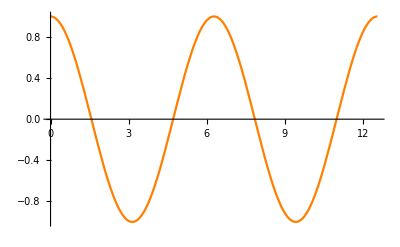

```mathematica
veloc1=Plot[ω*Cos[ ω x]/. ω-> 1,{x,0, 4 Pi}, PlotStyle->Orange]
```

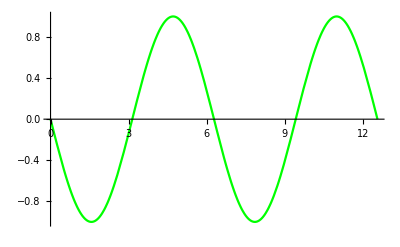

```mathematica
acel1=Plot[ω^2*(-Sin[ω x])/. ω-> 1,{x,0, 4 Pi}, PlotStyle->Green]
```

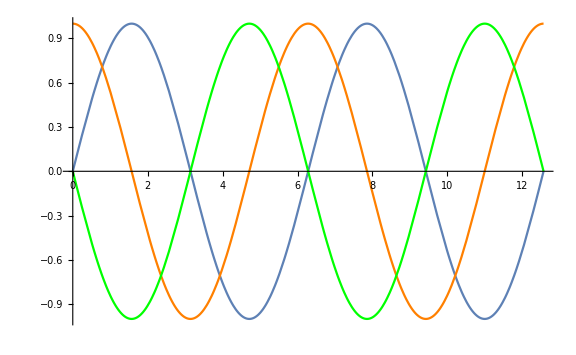

```mathematica
Show[posic,veloc,acel,ImageSize->Large]
```

Los desfases respectivos de la velocidad y aceleración con respecto a la posición son :

d_1= π/2 ; d_2=π ;   y también   p_v= p_p=p_a=1/(2π)

2) Movimiento Oscilatorio a lo largo de X (ω = 5)

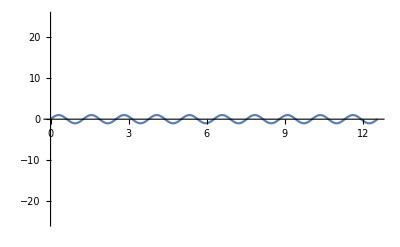

```mathematica
posic2=Plot[Sin[ ω x]/. ω-> 5,{x,0,4 Pi},PlotRange->{-25,25}]
```

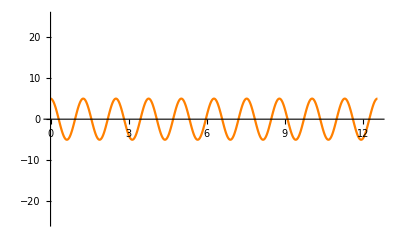

```mathematica
veloc2=Plot[ω*Cos[ ω x]/. ω-> 5,{x,0, 4 Pi}, PlotStyle->Orange,PlotRange->{-25,25}]
```

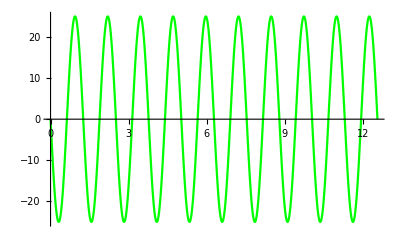

```mathematica
acel2=Plot[ω^2*(-Sin[ω x])/. ω-> 5,{x,0, 4 Pi}, PlotStyle->Green,PlotRange->{-25,25}]
```

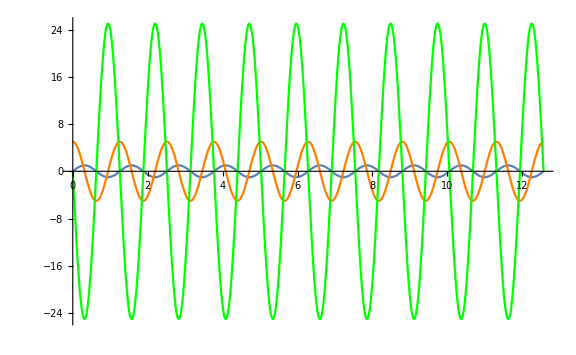

```mathematica
Show[posic2,veloc2,acel2,ImageSize->Large]
```

Los desfases respectivos de la velocidad y aceleración con respecto a la posición son:

d_1= π/10; d_2=π/5 ;  y también   p_v=p_p=p_a=1/(10π)

3) Movimiento Oscilatorio a lo largo de X (ω = 0.2)

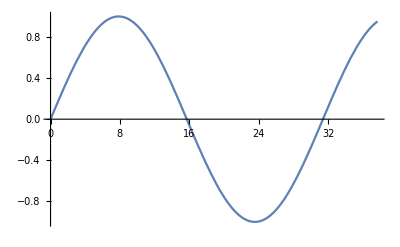

```mathematica
posic3=Plot[Sin[ ω x]/. ω-> .2,{x,0, 12 Pi},PlotRange->{-1,1}]
```

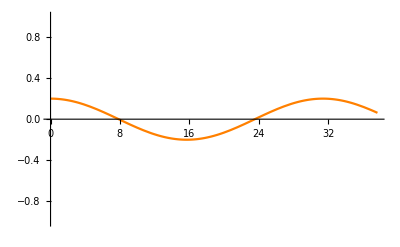

```mathematica
veloc3=Plot[ω*Cos[ ω x]/. ω-> .2,{x,0, 12 Pi}, PlotStyle->Orange,PlotRange->{-1,1}]
```

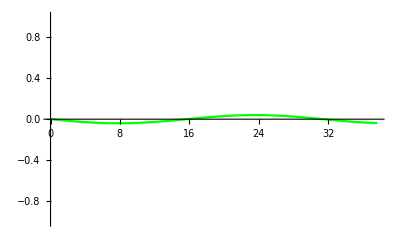

```mathematica
acel3=Plot[ω^2*(-Sin[ω x])/. ω-> .2,{x,0, 12 Pi}, PlotStyle->Green,PlotRange->{-1,1}]
```

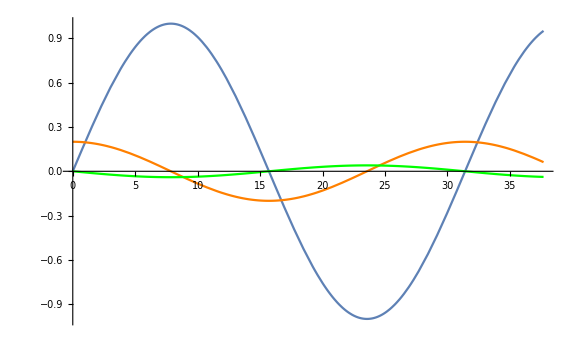

```mathematica
Show[posic3,veloc3,acel3,ImageSize->Large]
```

Los desfases respectivos de la velocidad y aceleración con respecto a la posición son :

d_1= (5π)/2; d_2=5π;   y también   p_v=p_p=p_a=5/(2π)